## Lab 3: Performance modelling

In this assignment you are going to develop an analytic model with the objective to study the performance with respect to total delay of airplanes from arrival to take-off. 

The airport in this assignment (same as in lab 1 and 2) can be modelled as a network of queues, which means that under certain assumptions the Jackson’s theorem [Chapter 6 in the textbook] applies and a Jackson network model can be developed.   Before the Jackson network model is developed, you are going to model a loss system and single queue systems.

The assignment is going to be solved by use of Mathematica.  All questions and answers should be given in this notebook, which contains some useful hints and examples of commands that might help you getting started.  Task 1 is a warm up. 
Note! At the end of this notebook you find a section called “Functions and hints” which can be very useful when editing the notebook, and tips about functions available.  For other questions, visit Wolfram for help and tutorials, and use the buildin help function which is also very useful.

How to access Mathematica (details on BB under “Mathematica”)
1. At Sahara it is installed
2. calcfarm has Mathematica installed (access via a remote desktop client, see https://innsida.ntnu.no/wiki/-/wiki/English/Software+Farm)
3. Install Mathematica on your computer (v12 or v11) and connect to the licence-server when start up (first time).  Note! You have to be at campus or using vpn to get access to the licence server
4. Backup solution if vpn fails: “%> ssh -Y sahara01 ...sahara30 (not all are connected so just try) - this solution is slow but can be used when there is a problem with vpn

### Task 1: Analytic solution of small birth-death Markov chain using Mathematica (Warm up) [0%]

The example in this section demonstrates how to : 
1) Set up the equations that are needed to obtain the steady state probabilities 
2) Determine performance measures from the steady state probabilities (e.g., utilization, loss, expected number) 
A few useful functions and tricks are included.

Task : Run through the example step by step.

The example is a two server system with no queue (M/M/2/2).


-Graphics-

Define the state variables - put them in a table

```mathematica
vars = {Subscript[p, 0],Subscript[p, 1],Subscript[p, 2]}; (* shift + ctrl gives subscript *)
```

Set of equations

```mathematica
eqn = {
λ Subscript[p, 0] == μ Subscript[p, 1],
λ Subscript[p, 1] == 2μ Subscript[p, 2],
Subscript[p, 0]+Subscript[p, 1]+Subscript[p, 2]==1} (* = and = gives == *)
```

{λ p_0==μ p_1,λ p_1==2 μ p_2,p_0+p_1+p_2==1}

Analytic solution

```mathematica
sol=Solve[eqn,vars] // Flatten (* Flatten to reduce the levels of nested vector/sets - just try with and without *)
```

{p_0→(2 μ^2)/(λ^2+2 λ μ+2 μ^2),p_1→(2 λ μ)/(λ^2+2 λ μ+2 μ^2),p_2→λ^2/(λ^2+2 λ μ+2 μ^2)}

Define a set of parameter values to obtain the numerical solution

```mathematica
para = {λ-> 0.9,μ-> 1.0} (* - followed by > gives -> *)
```

{λ→0.9,μ→1.}

Numerical solution : /. means apply rule ("para" in this case) to the set/vector "sol"

```mathematica
nsol = sol /. para (* try with different parameters in "para" *)
```

{p_0→0.433839,p_1→0.390456,p_2→0.175705}

Obtain performance measures
- Utilisation (util) is equal to probability that server is non - empty
- Loss (loss) is the probability that all (both) resources are taken (time congestion)

```mathematica
util = 1-Subscript[p, 0] 
loss = Subscript[p, 2]
```

1-p_0

p_2

- Expected number of servers in used (exp) - calculated in five different ways

```mathematica
exp = 0 Subscript[p, 0] + 1 Subscript[p, 1] + 2 Subscript[p, 2] 
exp = Sum[i Subscript[p, i],{i,0,2}]
exp = ∑_{i,0,2} i Subscript[p, i]
exp = {0,1,2} . vars 
exp = Range[0,2] . vars
```

p_1+2 p_2

p_1+2 p_2

p_1+2 p_2

«2 more identical outputs»

Use of Map (/@)  function

```mathematica
(* Make a set of numbers from 0 to 2 *)
Range[0,2]
(* Make a set of 1 *)
Table[1,{3}]
(* Make a set of Subscript[p, i] for i=0,1,2 *)
Subscript[p, #] & /@ Range[0,2] 
(* Summarise all elements in a set by vector multiplication *)
(Subscript[p, #] & /@ Range[0,2]) . Table[1,{3}]
(* Expected value "exp" again *) 
(# Subscript[p, #] & /@ Range[0,2]) . Table[1,{3}]
```

{0,1,2}

{1,1,1}

{p_0,p_1,p_2}

p_0+p_1+p_2

p_1+2 p_2

Substitute the p_i’s in util, loss, and exp with the solution from sol  and nsol

```mathematica
(* Apply rule, "sol" to obtain the symbolic experession *)
aexp = exp /. sol
(* Simplify *)
aexp = exp /. sol//Simplify
aloss = loss /. sol//Simplify
autil = util /. sol //Simplify
(* Apply rule, "nsol" to obtain the numerical experession *)
nexp = exp /. nsol
nloss = loss /. nsol
nutil = util /. nsol
```

(2 λ^2)/(λ^2+2 λ μ+2 μ^2)+(2 λ μ)/(λ^2+2 λ μ+2 μ^2)

(2 λ (λ+μ))/(λ^2+2 λ μ+2 μ^2)

λ^2/(λ^2+2 λ μ+2 μ^2)

(λ (λ+2 μ))/(λ^2+2 λ μ+2 μ^2)

0.741866

0.175705

0.566161

Define a function
i) Example : CDF of NegExp
ii) Function to obtain loss, utilisation and expected values when the set of state probabilities is known.
a = arrival intensity, b = server rate
set = 
i)  {0,0,1} : loss
ii) {0,1,1} : util
iii){0,1,2} : exp

```mathematica
(* CDF of negative exponential distribution with intensity λ *)
F[t_] := 1 - Exp[-λ t]
```

1-ⅇ^(-t λ)

1-ⅇ^-t

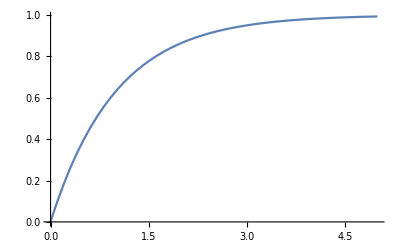

Piecewise[{{1-ⅇ^(-t λ), t≥0}, {0, True}}]

```mathematica
F[t]
F[t] /. {λ->1}
Plot[F[t] /. {λ->1}, {t,0,5}]
(* NOTE: this function already exists in Mathematica *) 
CDF[ExponentialDistribution[λ],t]
```

```mathematica
(* Function to obtain loss, utilisation and expected values (the "set" is different depending on what you are going to calculate) when the set of state probabilities is known. *) 
AGen[a_,b_,set_] := set . vars /. (sol /. {λ->a,μ->b})
```

Plot : utilisation (set={0,1,1}) and loss (set={0,0,1}) for different values of λ with μ = 1

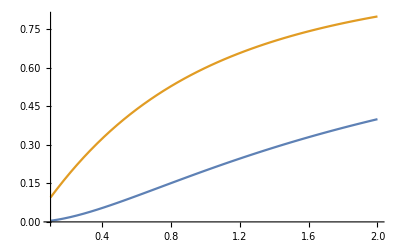

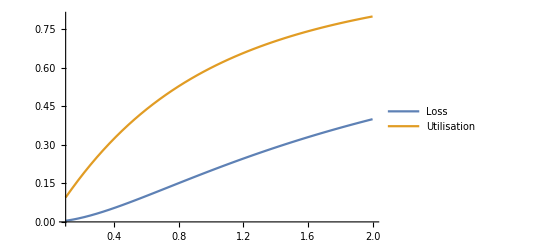

```mathematica
Plot[{AGen[λ,1,{0,0,1}],AGen[λ,1,{0,1,1}]},{λ,0.1,2}]
(* Think about why, for instance set={0,1,1} will give us the utilisation *)
Plot[{Legended[AGen[λ,1,{0,0,1}],"Loss"],Legended[AGen[λ,1,{0,1,1}],"Utilisation"]},{λ,0.1,2}]
```

### Task 2: Runways [25%]

Let the system state be the number of airplanes in landing and in the airspace over the airport. 
NOTE: Takeoffs are not included in this part of the assignment.
The airspace has a limited capacity. Arriving airplanes will be redirected if both runways are in use and the airspace is full. 
	2.1. Draw the Markov chain model for two runways (n=2) and N=10.  What kind of queue model is this in Kendall’s notation?
	 -Graphics-
	M/M/2/10/FIFO queue model

2.2. Set up the equations and solve them to determine the steady state probabilities for n=2 and N=10.

```mathematica
vars = Subscript[p, #] & /@ Range[0,10]
```

{p_0,p_1,p_2,p_3,p_4,p_5,p_6,p_7,p_8,p_9,p_10}

```mathematica
eqns = {
λ Subscript[p, 0] == μ Subscript[p, 1],
λ Subscript[p, 1] == 2μ Subscript[p, 2],
λ Subscript[p, 2] == 2μ Subscript[p, 3],
λ Subscript[p, 3] == 2μ Subscript[p, 4],
λ Subscript[p, 4] == 2μ Subscript[p, 5],
λ Subscript[p, 5] == 2μ Subscript[p, 6],
λ Subscript[p, 6] == 2μ Subscript[p, 7],
λ Subscript[p, 7] == 2μ Subscript[p, 8],
λ Subscript[p, 8] == 2μ Subscript[p, 9],
λ Subscript[p, 9] == 2μ Subscript[p, 10],
vars . Table[1,{11}]==1
};
sol=Solve[eqns,vars] //Flatten
```

{p_0→(512 μ^10)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_1→(512 λ μ^9)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_2→(256 λ^2 μ^8)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_3→(128 λ^3 μ^7)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_4→(64 λ^4 μ^6)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_5→(32 λ^5 μ^5)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_6→(16 λ^6 μ^4)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_7→(8 λ^7 μ^3)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_8→(4 λ^8 μ^2)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_9→(2 λ^9 μ)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_10→λ^10/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10)}

2.3. Solve the equations and obtain the expected number of runways in use and the expected number of planes in the airspace,as a function of λ {plot for λ∈[0.5, 5]} with μ=1.

Explain how and why the utilisation flattens out, and and argue for what you regard as an acceptable arrival rate λ.

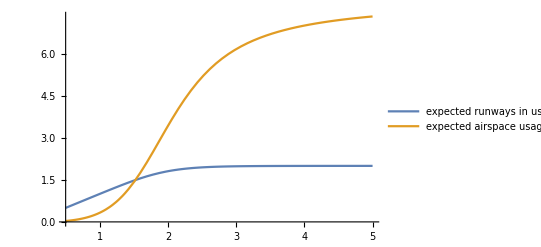

```mathematica
para = {n->2,N->10};
(*expRunways=∑_{i,0,N} Min[i,n]*Subscript[p, i] /.para*)
expRunwaysMask = {0,1,2,2,2,2,2,2,2,2,2};
expAirspaceMask = {0,0,0,1,2,3,4,5,6,7,8};
Plot[{Legended[AGen[λ,1,expRunwaysMask],"expected runways in use"],Legended[AGen[λ,1,expAirspaceMask],"expected airspace usage"]},{λ,0.5,5}]
```

The utilisation of the runways and the airspace flatten out because they fill up. The runways have a capacity of maximum 2 planes handled at the same time because each runway can handle one plane at a time. The expected value of runways flattens out when it reaches two because the moment a planes leaves the runway, a new plane from the airspace enters the runway. Based on the graph above, a lambda value between 2 and 3 would give acceptable waiting times for the runway without wasting resources. The most important thing to note is that a lambda value of around 5 will result in a full airspace and force the airport to reject planes. This should be avoided.

2.4. Plot the probability of redirected airplanes (n=2, N=10) as a function of λ ∈[0.5, 5] (with μ=1). 		
		Argue for what you regard as an acceptable arrival rate λ.

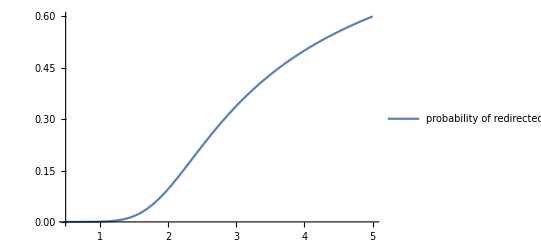

```mathematica
lossMask = {0,0,0,0,0,0,0,0,0,0,1};
Plot[{Legended[AGen[λ,1,lossMask],"probability of redirected planes"]},{λ,0.5,5}]
```

2.5. Make a function in Mathematica which implements Erlang's C formula (E_(2,n)(A) in Eq.(6.95) in the textbook). 
	Check that it returns E_(2,2)(A)=A^2/(2+A) (n=2 and where A=λ/μ).
	The probability of waiting  in a M/M/n -queue is given by Erlang’s C formula.

```mathematica
ErlC[A_,n_] := (((A^n)/n!)*n/(n-A))/(∑_{i,0,n-1} ((A^i)/i!)+(((A^n)/n!)*n/(n-A)))
```

```mathematica
para3 ={A->λ /μ };
erlangCTest = ErlC[A, 2] //Simplify
```

A^2/(2+A)

2.6. Use the appropriate formulas from Chapter 6 to obtain the expected (sojourn) time E[S] in the system when n=2 and N is infinite.
From Eq.(6.100) in the book we get the following function:

```mathematica
ExpSoujourn[A_,n_,μ_] := (1/((n-A)*μ))*(ErlC[A,n]+n-A)
```

2.7. Plot the probability that both runways are free as a function of λ ∈[1,3] (with μ=1) with N=10 and N infinite. (Comment results).

The probability that both runways are free is the same as p_0.

```mathematica
SteadyStateForMMn[A_,n_,i_] := If[i<n,((A^i)/i!)/(∑_{j,0,n-1} ((A^j)/j!)+(((A^n)/n!)*(n/(n-A)))) ,((A^i)/n!n^(i-n))/(∑_{j,0,n-1} ((A^j)/j!)+(((A^n)/n!)*(n/(n-A))))]
```

(2-λ)/(2+λ)

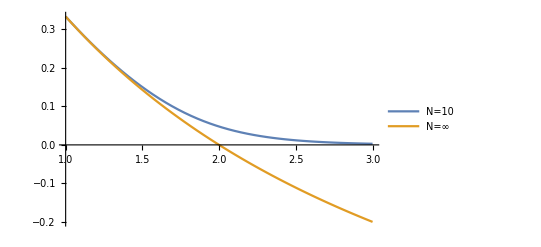

```mathematica
p0mmnNinf = SteadyStateForMMn[A,2,0] /. {A->λ /1 } //Simplify
emptyMaskN10 = {1,0,0,0,0,0,0,0,0,0,0};
Plot[{Legended[AGen[λ,1,emptyMaskN10],"N=10"], Legended[p0mmnNinf,"N=∞"]},{λ,1,3}]
```

With a finite queue there’s always the possibility that all planes in the airspace get to land before another plane arrives. This can be seen in the N = 10 graph where the probability is very low, but non-zero. However, as the other queue is infinite, the possibility is removed given that the queue will grow to infinity.

### Task 3: Deicing station [20%]

The objective in this task is to check the effect of changing the number of deicing stations, n. Assume infinite queuing capacity. 
	3.1. Draw the Markov chain model for n deicing stations. What kind of queue model is this in Kendall’s notation?
	for n =1
	-Graphics-
	M/M/n/∞/FIFO

3.2. Set up the equations and solve them to provide the steady state probabilities for n=1.

```mathematica
eqns3a[n_] := {
λ Subscript[p, 0] == μ Subscript[p, 1],
λ Subscript[p, 1] == Min[2, n]μ Subscript[p, 2],
λ Subscript[p, 2] == Min[3, n]μ Subscript[p, 3],
λ Subscript[p, 3] == Min[4, n]μ Subscript[p, 4],
λ Subscript[p, 4] == Min[5, n]μ Subscript[p, 5],
λ Subscript[p, 5] == Min[6, n]μ Subscript[p, 6],
λ Subscript[p, 6] == Min[7, n]μ Subscript[p, 7],
λ Subscript[p, 7] == Min[8, n]μ Subscript[p, 8],
λ Subscript[p, 8] == Min[9, n]μ Subscript[p, 9],
λ Subscript[p, 9] == Min[10, n]μ Subscript[p, 10],
vars . Table[1,{11}]==1
};
```

3.3. Use the functions from Queueing Processes to obtain the steady state probabilities for n=1 and n=2.
		Plot (use ListPlot) the steady state probabilities of states 0-10 for n=1 and n=2. (λ=0.07,μ=0.1). Compare and comment the difference between n=1 and n=2.

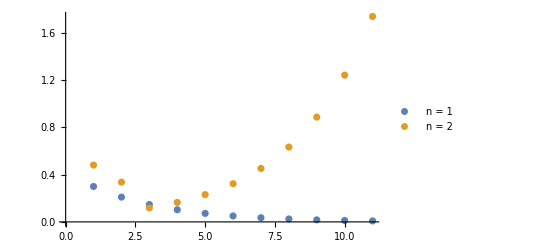

{1/(1+A+A^2/(2-A)),A/(1+A+A^2/(2-A)),A^2/(2 (1+A+A^2/(2-A))),A^3/(1+A+A^2/(2-A)),(2 A^4)/(1+A+A^2/(2-A)),(4 A^5)/(1+A+A^2/(2-A)),(8 A^6)/(1+A+A^2/(2-A)),(16 A^7)/(1+A+A^2/(2-A)),(32 A^8)/(1+A+A^2/(2-A)),(64 A^9)/(1+A+A^2/(2-A)),(128 A^10)/(1+A+A^2/(2-A))}

```mathematica
sol1=Solve[eqns3a[1],vars] //Flatten;
steadyState1 = Table[SteadyStateForMMn[A,1,i]/. {A->λ /μ }/. {λ-> 0.07} /. {μ-> 0.1},{i,0,10}] // Flatten;
sol2 = Solve[eqns3a[2], vars] // Flatten;
steadyState2 = Table[SteadyStateForMMn[A,2,i]/. {A->λ /μ  }/. {λ-> 0.07} /. {μ-> 0.1},{i,0,10}] // Flatten;
ListPlot[{Legended[steadyState1, "n = 1"], Legended[steadyState2, "n = 2"]}]
steadyState2 = Table[SteadyStateForMMn[A,2,i],{i,0,10}]
```

3.4. Use the functions from Queueing Processes to obtain a symbolic expression the time at deicing, E[S] for n.
	3.5. Plot the E[S] for n=1,..,10 (deicing stations), using the following parameters : {λ=0.1, μ=0.1}. How does the E[S] change with n?  How many  deicing stations would you recommend (argue)?

### Task 4: Turnaround at gate [15%]

After landing, the airplane is taxing to the gate where unloading and reloading take place, before the plane leaves the gate and is ready for takeoff.  The the expected turnaround time is 1/μ_t.  There is always a gate available for an arriving airplane.
	4.1. Suggest a queueing model for the gates (you may use Kendall’s notation)
	4.2. Obtain (on paper if you like) a symbolic expression for the steady state probabilities. What is this probability distribution called?
	4.3. Use the “QueueingProcess” to obtain the same steady state probabilities. 
	4.4. Plot the probability that n=0, 1, 2, 3, 4 gates are occupied. 
		(para = {λ→0.9,μ_t→1})
	4.5. Obtain the E[W] (time in the system). Compare with the expected service time (1/μ_t) and comment on the result.

### Task 5: The airport in cold weather [40%]

In this task it is expected that you solve the problem without help from the assistants (only to clarify any ambiguities and typos) - you’re on your own... 

In our system (the airport), an airplane needs 
	- access to a runway twice (landing and takeoff), 
	- a gate for turnaround of passengers and goods, 
	- and in case of cold weather it also needs a deicing station.  
In this task you should assume that there is cold weather (but no snow). The runways are shared between landing and takeoff and in this analytic model we assume no priority between the two.

Model the total “life cycle” of an airplane a network of queues using the Jackson’s theorem 
[[Mathematica has a “QueueingNetworkProcess” which is useful]].
	5.1. Explain how to apply the Jackson’s theorem and list the assumptions
	5.2. What are the “customers” and “nodes” in the system?
	5.3. Suggest  a  queue  model  type  (M/M/?)  for each node  (the nodes might need different kinds of queue model)?
	5.4. Draw the model (show the network of queues and indicate what type of queue you have in each node)
	5.5. Define the total arrival intensity for each of the queues (nodes) in the network of queues
	5.6. Apply “QueueingNetworkProcess” to specify the network model
	5.7. What is the probability that both runways are idle? 
		What is the probability that there are 4 airplanes?
		What is the probability that one airplane is at the deicing station?
	5.8. Obtain an expression for the expected number of airplanes in at the airport
	5.9. Obtain an expression for the expected time at the airport, E[S_a].
	5.10. Plot the expected time at the airport for different λ values.  
		Argue for what you regard as an acceptable arrival rate λ wrt. to total time at airport for an airplane.  
	5.11 Investigate where the bottleneck is and discuss which changes can be made (in service rates, resource capacities) if the arrival intensity λ is fixed and the total time at the airport  E[S_a] is regarded as too high.

## Functions and hints

#### “Queueing Processes” from Mathematica

See : https://reference.wolfram.com/language/guide/QueueingProcesses.html  
Queueing Process Models
	QueueingProcess — represents a queue with general arrival and service distributions
	QueueingNetworkProcess — represents a network of connected queues
Performance Measures
	QueueProperties[data] — steady-state and other properties for queues
	ErlangB - Erlang-B loss formula
	ErlangC - Erlang-C delay formula

List content of function

```mathematica
?QueueingProcess
```

Example with M/M/2/4

```mathematica
QueueingProcess
```

QueueingProcess

```mathematica
𝒫= {λ-> 0.5,μ->1};
(* Example with M/M/2/4 *) 
𝒬 = QueueingProcess[λ,μ,2,4];
(* List all properties of M/M/2/4 *)
QueueProperties[𝒬] //Simplify;
(* List MeanSystemTime of M/M/2/4 *)
QueueProperties[𝒬,"MeanSystemTime"] //Simplify;
𝒟 = StationaryDistribution[𝒬];
Subscript[π, x_] := PDF[𝒟,x];
Subscript[π, #]&/@Range[0,4] (* same as writing {Subscript[π, 0],Subscript[π, 1],Subscript[π, 2],Subscript[π, 3]} - try it *) 
(* Numerical probablity of Subscript[π, 4]*)
Probability[n== 4, n\[Distributed]𝒟] /.𝒫;
(* Numerical probablities of all states_*)
Probability[n== #, n\[Distributed]𝒟]& /@ Range[0,4];
(* Loss in M/M/4/4 *)
ErlangB[4,λ/μ] /.𝒫;
ErlangC[2,λ/μ] /. 𝒫
```

{(8 μ^4)/(λ^4+2 λ^3 μ+4 λ^2 μ^2+8 λ μ^3+8 μ^4),(8 λ μ^3)/(λ^4+2 λ^3 μ+4 λ^2 μ^2+8 λ μ^3+8 μ^4),(4 λ^2 μ^2)/(λ^4+2 λ^3 μ+4 λ^2 μ^2+8 λ μ^3+8 μ^4),(2 λ^3 μ)/(λ^4+2 λ^3 μ+4 λ^2 μ^2+8 λ μ^3+8 μ^4),λ^4/(λ^4+2 λ^3 μ+4 λ^2 μ^2+8 λ μ^3+8 μ^4)}

0.1

#### Some editing hints

Mathematical Notation Characters
https://reference.wolfram.com/language/guide/MathematicalNotationCharacters.html 

Special Characters
https : // reference.wolfram.com/language/guide/SpecialCharacters.html

```mathematica
(* esc+<something>+esc *)
(* ex ...*)
(* λ esc+l+esc *)
(* ∑ esc+\sum+esc *)
(* 𝒟 esc+scD+esc *) 
(* 𝒬 esc+scQ+esc*)
```

shift + return = evaluate the cell
; at then end will not return the result

Help function: 
1) Use : ?+function, e.g., ?Plot
2) Mouseover gives you:  - both a dropdown menu ,  and an info-button that takes you directly to the help page.

```mathematica
?Plot
```